# The generalized Langevin equation

## Background, motivation, formalism, and examples

## The Langevin equation

The Langevin equation is a Markovian stochastic differential equation concerns a particle diffuses in a potential. For a one-dimensional system, with position  and momentum   we have

is the conservative force on the particle,  is the coefficient of friction, and is random white-noise.   is essentially a Gaussian random variable which satisfies whose first and second moments are,

where the angled brackets denotes averages done over many samples. Eq. 3 simply means that samples of  at different times are independent of each other. Since these samples are independent, we say that the random noise term  is ‘Markovian’, meaning that the state (position and momentum) at  depends only on the current state at . Furthermore, for any system near thermal equilibrium, the random forces  and the friction constant  must be related

this relationship is called the (second) fluctuation-dissipation theorem and is characteristic of systems which obey linear response.

## The Ornstein-Uhlenbeck process

A common type of Langevin equation which may be solved analytically is the Ornstein-Uhlenbeck (OU) process. Understanding the OU process is important for the GLE as it allows us to embed the GLE dynamics into an extended Markovian phase space (more on this later). The simplest form of an OU process is a Langevin equation for a particle with no external potential.

Eq. 5 takes the form of a first-order linear inhomogeneous differential equation. Ignoring some subtleties about the integration of , we can solve Eq. 5 using standard methods such as integrating factors or the Laplace transform. For the integrating factors method we may multiply both sides by  which leads to,

Eq. 7 is the formal solution to Eq. 5 and this solution is what we call the “Ornstein-Uhlenbeck” process. Note that the OU process is also Gaussian, but it has a finite-correlation time,

Below I’ve included a short script for simulating trajectories from this OU process. Notice how they revert to the mean

ItoProcess[{{0.-p[t]},{{0.447214}},p[t]},{{p},{10}},{t,0}]

TemporalData[…]

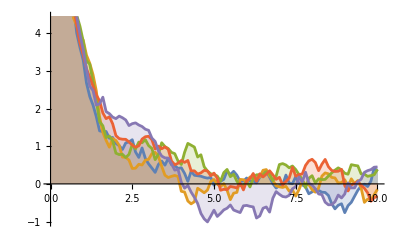

```mathematica
m = 1;
γ = 1;
kBT = 0.1;
p0 = 10;
proc=ItoProcess[ⅆp[t]==-γ p[t] ⅆt+Sqrt[2 m γ kBT ] ⅆw[t],p[t],{p,p0},t,w\[Distributed]WienerProcess[]]
RandomFunction[proc,{0,10,0.1},5]
ListLinePlot[%,Filling->Axis]
```

## The multivariate Ornstein-Uhlenbeck process

More generally we can define a vector-valued Ornstein-Uhlenbeck process via the stochastic differential equation:

Mathematica does not allow for bold math symbols, take care that  and  above are matrices. The fluctuation-dissipation theorem for such an equation takes the form,

where  is the stationary covariance matrix of the process. A simple example of a multivariate OU process is provided by the Langevin equation for a stochastic harmonic oscillator, which in matrix form can be expressed as:

(
x)=-(      | 
 | 0) (
x)+( | 0
0 | 0)(
)

We can make Eq. 12 more symmetric if we make a few substitutions. 1) Let , this makes the position and momenta coordinates have the same units. 2) Let . 3) Let . This leads to

(
)=-(      | 
 | 0) (
)+( | 0
0 | 0)(
)

Now applying the fluctuation-disssipation theorem (Eq. 11) we see

= ( | 
 | ) =   ( | 0
0 | )

Which does indeed satisfy equilibrium thermodynamics (i.e. equipartition theorem). 
In order to solve the multivariate OU process, we can use the same method of integrating factors, but we now must be careful as the matrices   and  do not necessarily commute,

Now solving for the time-correlation function we have

Now apply the fluctuation dissipation theorem (Eq. 11)

Eq. 17 is very important the subsequent sections on the generalized Langevin equation. For the stochastic harmonic oscillator we can solve for the matrix exponential, which yields:

```mathematica
Clear["Global`*"]
A = {{2γ,Sqrt[ ω^2 +γ^2]},{-Sqrt[ω^2 +γ^2],0}};
A //MatrixForm
FullSimplify[MatrixExp[-A*t]]//MatrixForm
```

(2 γ | √(γ^2+ω^2)
-√(γ^2+ω^2) | 0)

((ⅇ^(-t γ) (ω Cos[t ω]-γ Sin[t ω]))/ω | -(ⅇ^(-t γ) √(γ^2+ω^2) Sin[t ω])/ω
(ⅇ^(-t γ) √(γ^2+ω^2) Sin[t ω])/ω | (ⅇ^(-t γ) (ω Cos[t ω]+γ Sin[t ω]))/ω)

## The Generalized Langevin Equation

The generalized Langevin equation is a non-Markovian analog to the Langevin equation. For a one-dimensional system, with position  and momentum   we have

where  is the memory (non-Markovian friction) kernel and  is a random non-Markovian noise. The average of is zero and the second moments (correlation-functions) are determined by the fluctuation-dissipation theorem,

The Markovian friction constant  is recovered by integrating the memory kernel over time . For most choices of the memory kernel, the GLE cannot be solved analytically. A  common choice that can be solved analytically is the exponential memory case

This equation can be solved via the Laplace transform. The final form of the two-time correlation function (which I will not derive here, but can be found in chapter 15 of Tuckerman’s statistical mechanics) is

where .  Eq. 23 with the results of the Markovian stochastic oscillator (Eq. 19)  reveals how difficult it can be to determine whether a process is Markovian based solely on the analysis of it’s time correlation functions. We see that the time-correlation functions of a non-Markovian heat bath without an external potential are essentially can have the same functional form as the time-correlation functions of a Markovian harmonic oscillator.

## The extended variable transformation.

Practical simulation of the GLE requires sampling a correlated noise  and computing the memory integral . The latter is expensive in terms of both processing power and memory, especially for systems with long correlation times. On top of this, most MD codes do not support storing the state of the system in memory, which means implementing the memory kernel involves repetitive read/write commands to the disk which can slow a simulation down quite considerably. A solution to these problems is called the “extended-variable transformation”. In short, it involves mapping the non-Markovian dynamics of the GLE to a Markovian system in thermal contact with a multivariate Ornstein-Uhlenbeck process. To begin deriving these equations consider a memory kernel of the form  where  is some NxN matrix,  is an Nx1 column vector, and  is a 1xN row vector. Now we can express the entire memory integral as